```mathematica
Cos[k a]-Subscript[ϰ, 0]/k Sin[k a]/.k->ⅈ ϰ
```

Cosh[a ϰ]-(Sinh[a ϰ] ϰ_0)/ϰ

```mathematica
Plot[{1,-1,Table[Cosh[x]-(Sinh[x]a)/x,{a,0,5}]}//Flatten//Evaluate,{x,0,5},PlotStyle->{{Gray,Dashed},{Gray,Dashed},Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},PlotLegends->Placed[{None,None,"ϰ_0a=0","ϰ_0a=1","ϰ_0a=2","ϰ_0a=3","ϰ_0a=4","ϰ_0a=5"},{Left,Center}],AxesLabel->{a ϰ ,"ch(aϰ)-(sh (aϰ) SubscriptBox[aϰ, 0])/aϰ"}]
```

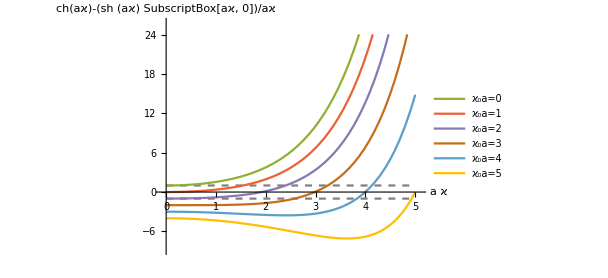

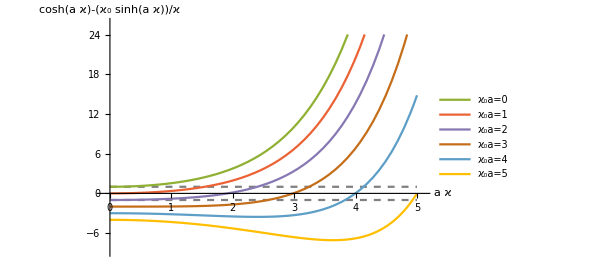

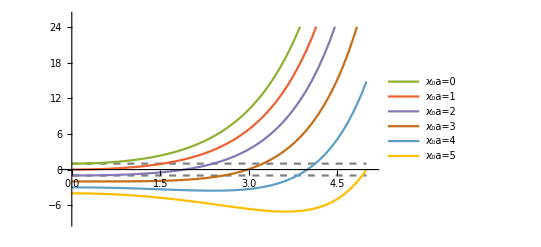

```mathematica
Solve[Cos[k a]== Cosh[a ϰ]-(Sinh[a ϰ] a Subscript[ϰ, 0])/(a ϰ),k]
```

{{k→ConditionalExpression[(-ArcCos[(ϰ Cosh[a ϰ]-Sinh[a ϰ] ϰ_0)/ϰ]+2 π C[1])/a, C[1]∈ℤ]},{k→ConditionalExpression[(ArcCos[(ϰ Cosh[a ϰ]-Sinh[a ϰ] ϰ_0)/ϰ]+2 π C[1])/a, C[1]∈ℤ]}}

```mathematica
Series[ArcCos[(ϰ Cosh[a ϰ]-Sinh[a ϰ] Subscript[ϰ, 0])/ϰ]/a,{Subscript[ϰ, 0],0,1}]//Normal
```

ArcCos[Cosh[a ϰ]]/a+(Sinh[a ϰ] ϰ_0)/(a ϰ √(1-Cosh[a ϰ]^2))

```mathematica
Simplify[ArcCos[Cosh[a ϰ]]/a+(Sinh[a ϰ] Subscript[ϰ, 0])/(a ϰ √(1-Cosh[a ϰ]^2))]
```

(ArcCos[Cosh[a ϰ]]+(Sinh[a ϰ] ϰ_0)/(ϰ √(-Sinh[a ϰ]^2)))/a

```mathematica
Solve[ Cosh[x]-(Sinh[x] 2)/x==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Cosh[x]-(2 Sinh[x])/x==0,x]

```mathematica
Cosh[x]-(Sinh[x] 2)/x/.x->2
```

```mathematica
N[Cosh[x]-Sinh[x]/.x->5]
```

0.00673795

```mathematica
N[Cosh[2]-Sinh[2]]
```

0.135335

```mathematica
Solve[Cos[k a]== Cosh[a ϰ]- a Subscript[ϰ, 0],k]
```

{{k→ConditionalExpression[(-ArcCos[Cosh[a ϰ]-a ϰ_0]+2 π C[1])/a, C[1]∈ℤ]},{k→ConditionalExpression[(ArcCos[Cosh[a ϰ]-a ϰ_0]+2 π C[1])/a, C[1]∈ℤ]}}

```mathematica
Series[Cosh[x]-(Sinh[x] a)/x,{x,0,1}]
```

(1-a)+O[x]^2

```mathematica
1/(2π)∫_(-∞)^∞ 1/(e+ p^2/(2m))ⅆp
```

ConditionalExpression[(√(1/(e m)) m)/(√2), Re[e m]≥0||e m∉ℝ]

```mathematica
Cos[k a]=Cos[ (√(2 m e))/ℏ a]-(Subscript[ϰ, 0] ℏ)/(√(2 m e))Sin[ (√(2 m e))/ℏ a]
```

```mathematica
1-(k a)^2/2=Cos[ (√(2 m e))/ℏ a]-(Subscript[ϰ, 0] ℏ)/(√(2 m e))Sin[ (√(2 m e))/ℏ a]
```

```mathematica
Solve[k==(√(2 m e))/ℏ+2π n/a,e]
```

{{e→(a^2 k^2 ℏ^2-4 a k n π ℏ^2+4 n^2 π^2 ℏ^2)/(2 a^2 m)}}

```mathematica
D[(a^2 k^2 ℏ^2-4 a k n π ℏ^2+4 n^2 π^2 ℏ^2)/(2 a^2 m), {k,2}]
```

ℏ^2/m